# Lindy Effect

## The Lindy Effect as an Absorbing Barrier

https://twitter.com/nntaleb/status/1073917828149985282
https://twitter.com/nntaleb/status/1342999782978158597
https://twitter.com/nntaleb/status/1146214203574968322

Write the contents relative both today and a well defined point in the past.
Write it to be relevant 30 years ago.
This will make it stay relevant to 30 years.
Time detects and produces fragility.
One can do negative forecasting. Collapses are easier to predict than what will emerge.

## Intuitions

Use a simpler model of arithmetic Brownian motion.
There is an absorbing barrier.
Introduce a drift term of μ = 0. This gives power law with tail exponent α = 1/2.
This power law must have an infinite mean.
Use a negative drift. Gives piecewise power law behavior, but is asymptotic,  non-power law.

```mathematica
data := RandomFunction[WienerProcess[0,1], {0, 10, 0.01}][[2]][[1]] // Flatten
```

```mathematica
?WienerProcess
```

Note that there is no drift.

```mathematica
stoppingtime[H_,X_] := Min[Position[Table[Boole[TrueQ[X[[i]]<H]]1, {i, 1, Length[data]}], 1]]
```

Setting stopping time to be -1 here, then force it to be -2 always if it hits -1.

```mathematica
XL = Table[X = data;
Table[If[i < stoppingtime[-1,X], X[[i]],-2],{i, Length[data]}],{14}];
```

We can plot the Wiener process as shown.

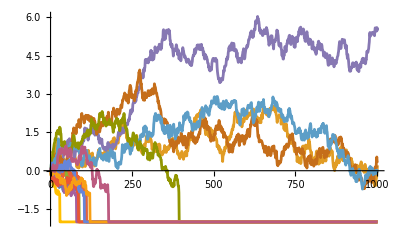

```mathematica
ListLinePlot[XL]
```

We are not dealing with stopping time τ but Max(τ,T).
The length of the data is T.
Take T → ∞.

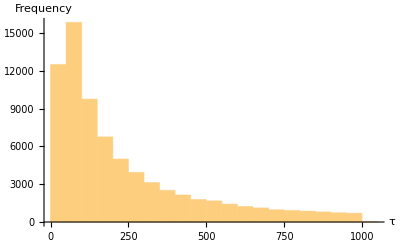

```mathematica
Histogram[Table[stoppingtime[-1,data],{10^5}], AxesLabel->{τ,"Frequency"}]
```

### Other Processes

```mathematica
Show[WolframLanguageData["WienerProcess","RelationshipCommunityGraph"],ImageSize->Full]
```

-Graphics-

```mathematica
?GeometricBrownianMotionProcess
```

## First Simplified Derivation Assuming Driftless Arithmetic Brownian Motion

Let X_t be a stochastic process with no drift satisfying dX = σ dB.
Let B be a Brownian motion where X_0=0.
We have X_t= X_0+σ√t W_(0,1), where W is a standardised normal random variable.
Let L < 0 be the level of the absorbing barrier (constant) hitting from above.
Let τ be the first passage time where τ = inf{t : X_t=L}
We have using the reflection principle the following  distribution of τ.
Take the survival function of X above L.
By definition we cannot have a conditional probabiity of hitting L with τ > t.
By symmetry, X is as likely to be above L and below L.
Accordingly the cumulative P(τ<t) = 2 P(X_t<L) = 2CDF(L). The distribution of τ is (∂P(τ<t))/(∂τ).

```mathematica
cum = 2CDF[NormalDistribution[0,σ Sqrt[τ]], L] // FunctionExpand
```

1+Erf[L/(√2 σ √τ)]

```mathematica
?D
```

Note that this is the distribution of τ.

```mathematica
Φ = D[cum, τ]
```

-(ⅇ^(-L^2/(2 σ^2 τ)) L)/(√(2 π) σ τ^(3/2))

```mathematica
hf=-D[Log[1-cum], τ]
```

(ⅇ^(-L^2/(2 σ^2 τ)) L)/(√(2 π) σ τ^(3/2) Erf[L/(√2 σ √τ)])

The plot shows how there just a difference in absorbing barrier

General::munfl: Exp[-1223.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4895.1] is too small to represent as a normalized machine number; precision may be lost.

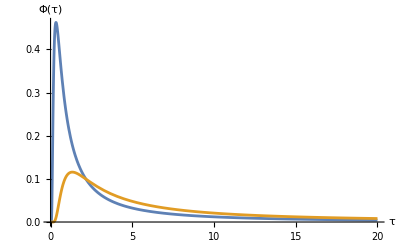

```mathematica
Plot[{Φ/.{σ->1,L->-1}, Φ/.{σ->1,L->-2}},{τ,0,20}, PlotRange->All, AxesLabel->{τ,"Φ(τ)"}]
```

This is a power law with half tail exponent.
Take the logarithm of the survival function.

General::munfl: Exp[-1223.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4895.1] is too small to represent as a normalized machine number; precision may be lost.

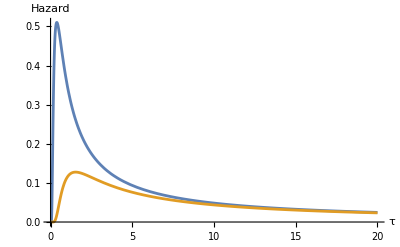

```mathematica
Plot[{hf/.{σ->1,L->-1}, hf/.{σ->1,L->-2}},{τ,0,20}, PlotRange->All, AxesLabel->{τ,"Hazard"}]
```

```mathematica
Limit[Log[1-cum]/Log[τ],τ->Infinity, Assumptions -> σ>0]
```

-1/2

Girsanov change of measure for negative drift.